```mathematica
MatrixPower[({{0.6, 0.3}, {0.4, 0.7}}),100].({{1}, {0}})
```

{{0.428571},{0.571429}}

```mathematica
f[x_]:=MatrixPower[({{0.25, 0.1, 0.05}, {0.25, 0.3, 0.15}, {0.5, 0.6, 0.8}}),x].({{1}, {0}, {0}})
```

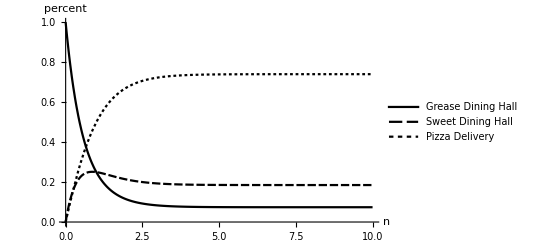

```mathematica
Plot[{f[x][[1,1]],f[x][[2,1]],f[x][[3,1]]},
{x,0,10},
AxesLabel->{"n","percent"},
PlotLegends->{"Grease Dining Hall","Sweet Dining Hall","Pizza Delivery"},
PlotTheme->"Monochrome"]
```

```mathematica
Total[f[100]]
```

{1.}

```mathematica
f4[x_]:=MatrixPower[({{0.35, 0.1}, {0.65, 0.9}}),x].({{1}, {0}})
```

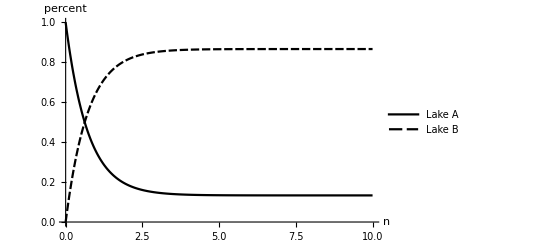

```mathematica
Plot[{f4[x][[1,1]],f4[x][[2,1]]},
{x,0,10},
PlotRange->{0,1},
AxesLabel->{"n","percent"},
PlotLegends->{"Lake A","Lake B"},
PlotTheme->"Monochrome"]
```

```mathematica
f4[10]
```

{{0.133334},{0.866666}}

```mathematica
0.995+0.995-0.995 0.995
```

0.999975

```mathematica
(0.99 0.999)+0.998-(0.99 0.999) 0.998
```

0.999978

```mathematica
(0.99 0.99)+(0.99 0.99)-(0.99 0.99) (0.99 0.99)
```

0.999604

```mathematica
0.993 0.999975 0.999978 0.98 0.999604
```

0.972709

```mathematica
1-(1-0.99)(1-0.999)(1-0.998)
```

1.

```mathematica
NumberForm[0.99999998,16]
```

0.99999998

```mathematica
0.998 0.999975 1 0.98 1
```

0.978016